# Game of Life is universal (version 22-10-2020)

### The “Game of Life” rule: binary (0: live cell; 1: dead cell), Moore neighbourhood with radius = 1

### Game of Life is outer-totalistic (and not totalistic)

#### Game of Life is not Totalistic :

— From state transition 1:  =3  ⇒ 1
— From state transition 2:  >(3+1)  ⇒ 0 
— From state transition 3:  <(2+1)  ⇒ 0 
— From state transition 4:  =(2+1) or =(3+1)  ⇒ 1
— From state transition 5:  ≠3  ⇒ 0

Here’s a contradiction:
— From state transition 4:  =(3+1) ⇒ 1
— From state transition 5:  =4         ⇒ 0

### Implementation in Mathematica: outer-totalistic rule 224

```mathematica
GameOfLife={224,{2,{{2,2,2},{2,1,2},{2,2,2}}},{1,1}};
```

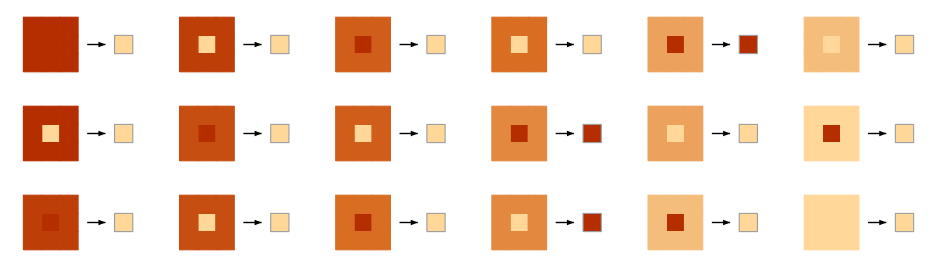

```mathematica
RulePlot[CellularAutomaton[GameOfLife],PlotTheme->"VibrantColor"]
```

```mathematica
Puffer={{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}
```

{{1,4},{2,5},{3,1},{3,5},{4,2},{4,3},{4,4},{4,5},{8,1},{9,2},{9,3},{10,3},{11,3},{12,2},{15,1},{15,4},{16,5},{17,1},{17,5},{18,2},{18,3},{18,4},{18,5}}

```mathematica
ListAnimate[ArrayPlot[#]&/@CellularAutomaton[GameOfLife,{SparseArray[Puffer->1],0},500]]
```

### Implementation in Mathematica: special named rule “GameOfLife”

```mathematica
ListAnimate[ArrayPlot[#]&/@CellularAutomaton["GameOfLife",{SparseArray[Puffer->1],0},500]]
```

### Implementation in Mathematica: the rule number in its corresponding space

```mathematica
2^(2^9)
```

13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084096

```mathematica
FromDigits[
Last/@
Reverse@
SortBy[
Switch[#⟦5⟧,
0,Module[{C01s=Count[Drop[#,{5}],1]},If[C01s==3,{#,1},{#,0}]],
1,Module[{C11s=Count[Drop[#,{5}],1]},If[C11s>3∨C11s<2,{#,0},{#,1}]]
]&/@Tuples[{0,1},9],
First],
2]
```

47634829485252037513200973884082471888288955642325528262910887637847274372981720534370017768342996036219492316860704401273651054628223608960

```mathematica
ListAnimate[ArrayPlot[#]&/@CellularAutomaton[{47634829485252037513200973884082471888288955642325528262910887637847274372981720534370017768342996036219492316860704401273651054628223608960,2,{1,1}},{SparseArray[Puffer->1],0},500]]
```

### The Glider

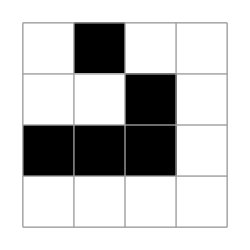
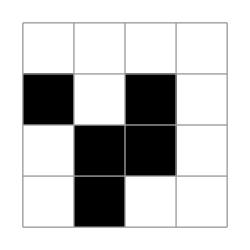
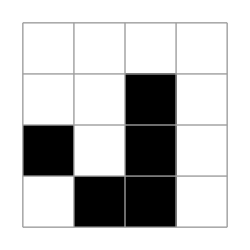
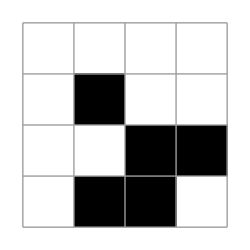
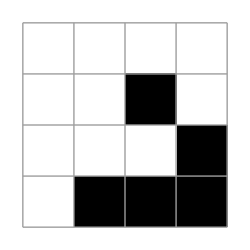

```mathematica
ArrayPlot[#,ImageSize->250,Mesh->True]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},4]
```

```mathematica
ListAnimate[ArrayPlot[#,ImageSize->250,Mesh->True]&/@CellularAutomaton["GameOfLife",{{{0,1,0},{0,0,1},{1,1,1}},0},20]]
```

### Game of Life is universal